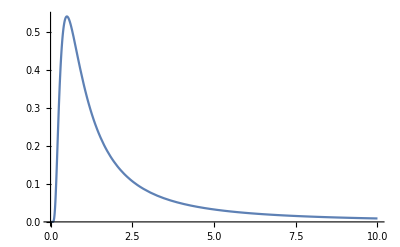

```mathematica
Plot[Exp[-1/x]/(x^2),{x,0,10}, PlotRange->Full]
```

```mathematica
f[T_]:=((N*e^2)/(k*T^2))*Exp[-e/(T*k)]
```

```mathematica
f'[T]
```

(e^3 ⅇ^(-e/(k T)) N)/(k^2 T^4)-(2 e^2 ⅇ^(-e/(k T)) N)/(k T^3)

```mathematica
Simplify[(e^3 ⅇ^(-e/(k T)) N)/(k^2 T^4)-(2 e^2 ⅇ^(-e/(k T)) N)/(k T^3)]
```

(e^2 ⅇ^(-e/(k T)) N (e-2 k T))/(k^2 T^4)

```mathematica
e
```

e

```mathematica
Solve[(e^3 ⅇ^(-e/(k T)) N)/(k^2 T^4)-(2 e^2 ⅇ^(-e/(k T)) N)/(k T^3)==0,T]
```

{{T→e/(2 k)}}

```mathematica
f[e/(2 k)]
```

(4 k N)/ⅇ^2

```mathematica
Solve[Exp[1/T]==(((U/e)+N)^(k/e))*(((U/e)+N)^(k*N))/((U/e)^(k/e)), U]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(1/T)==(U/e)^(-k/e) (N+U/e)^(k/e+k N),U]

```mathematica
F[U_]=k*(((U/c)+N)*Log[(U/c)+N]-(U/c)*Log[U/c]-N*Log[N])
```

k (-N Log[N]-(U Log[U/c])/c+(N+U/c) Log[N+U/c])

```mathematica
Simplify[k (-N Log[N]-(U Log[U/e])/e+(N+U/e) Log[N+U/e])]
```

-(k (e N Log[N]+U Log[U/e]-(e N+U) Log[N+U/e]))/e

```mathematica
F'[U]
```

k (-Log[U/c]/c+Log[N+U/c]/c)

```mathematica
Simplify[k (-Log[U/c]/c+Log[N+U/c]/c)]
```

(k (-Log[U/c]+Log[N+U/c]))/c

```mathematica
Simplify[k (-Log[U/e]/e+Log[N+U/e]/e)]
```

(k (-Log[U/e]+Log[N+U/e]))/e

```mathematica
Solve[1/T==k (-Log[U/c]/c+Log[N+U/c]/c),U]
```

{{U→(c N)/(-1+ⅇ^(c/(k T)))}}

```mathematica
g[T_]:=(c N)/(-1+ⅇ^(c/(k T)))
```

```mathematica
g'[T]
```

(c^2 ⅇ^(c/(k T)) N)/((-1+ⅇ^(c/(k T)))^2 k T^2)

```mathematica
FullSimplify[(c^2 ⅇ^(c/(k T)) N)/((-1+ⅇ^(c/(k T)))^2 k T^2)]
```

(c^2 N Csch[c/(2 k T)]^2)/(4 k T^2)

```mathematica
TrigReduce[(c^2 N Csch[c/(2 k T)]^2)/(4 k T^2)]
```

(c^2 N)/(2 k T^2 (-1+Cosh[c/(k T)]))

```mathematica
Simplify[(c^2 N)/(2 k T^2 (-1+Cosh[c/(k T)]))]
```

(c^2 N Csch[c/(2 k T)]^2)/(4 k T^2)